# Input for meta-community simulations

```mathematica
LandscapeFile="/Users/ailenemacpherson/Documents/VisualStudio/metacommunity/landscape_df.csv";
```

```mathematica
ExportFile="/Users/ailenemacpherson/Documents/VisualStudio/metacommunity/input.txt";
```

### Number of generations

```mathematica
gmax=400;
```

## Landscape

### Entering landscape

```mathematica
land=Import[LandscapeFile][[2;;,-3;;]];
```

```mathematica
xmax=land[[;;,2]]//Max;
```

```mathematica
ymax=land[[;;,3]]//Max;
```

```mathematica
LMtrx:=Block[{c,out},out=Table[0,{y,1,xmax},{x,1,xmax}];
For[c=1,c≤Length[land],c++,
out[[land[[c,3]],land[[c,2]]]]=land[[c,1]];
];
out
]
```

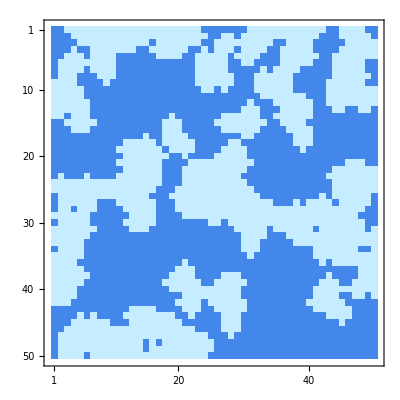

```mathematica
MatrixPlot[LMtrx,ColorFunction->"DeepSeaColors"]
```

```mathematica
LString[file_]:=LString[file]=Block[{x,y,out},out="";
For[y=1,y≤ymax,y++,
For[x=1,x≤xmax,x++,
out=out<>ToString[LMtrx[[y,x]]]<>" "
];
out=out<>"\n"
];
out
];
```

```mathematica
LString["landscape_df.csv"];
```

## Initial conditions

### Number of species

Number of plant species nb

```mathematica
nb=5;
```

number of herbivore species nh

```mathematica
nh=3;
```

number of predator species np

```mathematica
np=2;
```

### Initial Density

```mathematica
bTot0=1000;
hTot0=100;
pTot0=50;
```

```mathematica
hInitS=RandomChoice[Flatten[LMtrx/Total[Total[LMtrx]]//N]->Flatten[Table[{x,y},{y,1,ymax},{x,1,xmax}],1],hTot0];
pInitS=RandomChoice[Flatten[LMtrx/Total[Total[LMtrx]]//N]->Flatten[Table[{x,y},{y,1,ymax},{x,1,xmax}],1],pTot0];
```

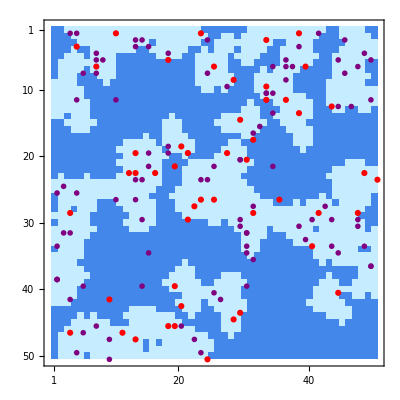

```mathematica
hInitS2=Table[{hInitS[[e,1]],ymax-hInitS[[e,2]]},{e,1,Length[hInitS]}];
pInitS2=Table[{pInitS[[e,1]],ymax-pInitS[[e,2]]},{e,1,Length[pInitS]}];
Show[{MatrixPlot[LMtrx,ColorFunction->"DeepSeaColors"],ListPlot[hInitS2,PlotStyle->Purple,PlotMarkers->•],ListPlot[pInitS2,PlotStyle->Red]}]
```

### Initial energy

```mathematica
e0=8;
```

## Parameters

### Food web matrices

αMtrx[[i,j]] gives the competitive effect of plant species j on the growth of plant species i.

```mathematica
intra=1;
interMax=1;
interMin=1;
```

```mathematica
αMtrx=Block[{out,i1,i2},out=Table[0,{i1,1,nb},{i2,1,nb}];
For[i1=1,i1≤nb,i1++,
For[i2=1,i2≤nb,i2++,
out[[i1,i2]]=If[i1==i2,intra,RandomReal[{interMin,interMax}]];
]
];
out];
```

βMtrx[[i,j]] is the probability that herbivore j eats plant species i

```mathematica
βMtrx=Block[{out,i,j},out=Table[0,{i,1,nb},{j,1,nh}];
For[i=1,i≤nb,i++,
For[j=1,j≤nh,j++,
out[[i,j]]=RandomReal[{0.0,0.05}];
]
];
out];
```

```mathematica
βMtrx
```

{{0.0272554,0.0303772,0.0158636},{0.0455748,0.0224128,0.0457196},{0.0241237,0.0399063,0.0196607},{0.0499433,0.0105475,0.00212399},{0.042041,0.0393564,0.0425622}}

γMtrx[[j,k]] is the probability that predator k eats herbivore j

```mathematica
γMtrx=Block[{out},out=Table[0,{j,1,nh},{k,1,np}];
For[j=1,j≤nh,j++,
For[k=1,k≤np,k++,
out[[j,k]]=RandomReal[{0.0,0.1}];
]
];
out];
```

```mathematica
γMtrx
```

{{0.00431565,0.0589458},{0.00553033,0.0993448},{0.0284329,0.0796932}}

### Intra-specific deterrence

```mathematica
αH=0.002;
αP=0.002;
```

### Growth and abiotic effects

Growth rate of biomass

```mathematica
r=0.5;
```

Carrying capacity of biomass per deme

```mathematica
k=1;
```

θ environmental optima

```mathematica
θ=10;
```

Environmental sensitivity

```mathematica
σ=3;
```

Conversion rate of herbivores

```mathematica
ch=60;
```

conversion rate of predators

```mathematica
cp=60;
```

Energy per offspring herbivores

```mathematica
ρh=e0*1;
```

Energy per offspring predator

```mathematica
ρp=e0*1;
```

reproductive investment herbivores (between 0 and 1)

```mathematica
ξh=0.5;
```

reproductive investment predators (between 0 and 1)

```mathematica
ξp=0.5;
```

### Movement

Movement probability

```mathematica
m=0.8;
```

Error rate

```mathematica
ϵhMax=0.1;
ϵpMax=0.1;
```

Decay

```mathematica
dh=0.005;
dp=0.001;
```

```mathematica
Exp[-dh 1]
```

0.995012

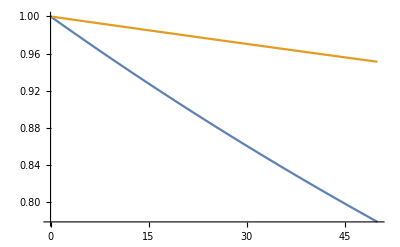

```mathematica
Plot[{Exp[-dh x],Exp[-dp x]},{x,0,xmax},PlotRange->All]
```

ψ Weights (Abioitic, herbivory, predation)

```mathematica
ψW={0.2,0.6,0.2};
```

## Making input files

### Landscape

```mathematica
out="Input file for metacommunity simulations:\n";
out=out<>"Number of generations (gmax): "<>ToString[gmax]<>"\n";
out=out<>"LANDSCAPE:\n";
out=out<>"X dimension (xmax): "<>ToString[xmax]<>"\n";
out=out<>"Y dimension (ymax): "<>ToString[ymax]<>"\n";
out=out<>"Landscape Matrix (LMtrx):\n";
out=out<>LString["landscape_df.csv"];
```

### Initial conditions

```mathematica
out2=out<>"\n INITIAL CONDITIONS:\n";
out2=out2<>"Number of plant species (nb): "<>ToString[nb]<>"\n";
out2=out2<>"Number of herbivore species (nh): "<>ToString[nh]<>"\n";
out2=out2<>"Number of predator species (np): "<>ToString[np]<>"\n";
out2=out2<>"Initial biomass (bTot0): "<>ToString[bTot0]<>"\n";
out2=out2<>"Initial herbivore density (hTot0): "<>ToString[hTot0]<>"\n";
out2=out2<>"Initial herbivore locations/type (hInitMtrx):\n";
Module[{r,c},
For[r=1,r≤2,r++,
For[c=1,c≤hTot0,c++,
out2=out2<>ToString[hInitS[[c,r]]-1]<>" "
];
out2=out2<>"\n"
];
For[c=1,c≤hTot0,c++,
out2=out2<>ToString[RandomInteger[{0,nh-1}]]<>" "
];
out2=out2<>"\n"
];
out2=out2<>"Initial predator density (pTot0): "<>ToString[pTot0]<>"\n";
out2=out2<>"Initial predator locations (pInitMtrx):\n";
Module[{r,c},
For[r=1,r≤2,r++,
For[c=1,c≤pTot0,c++,
out2=out2<>ToString[pInitS[[c,r]]-1]<>" "
];
out2=out2<>"\n"
];
For[c=1,c≤pTot0,c++,
out2=out2<>ToString[RandomInteger[{0,np-1}]]<>" "
];
out2=out2<>"\n"
];
out2=out2<>"Initial energy (energy0): "<>ToString[e0]<>"\n";
```

### Parameters

```mathematica
out1=out2<>"\n PARAMETERS: \n";
out1=out1<>"alpha Matrix (alphaMtrx):\n";
Module[{r,c},
For[r=1,r≤nb,r++,
For[c=1,c≤nb,c++,
out1=out1<>ToString[αMtrx[[r,c]]]<>" "
];
out1=out1<>"\n"
]
];
out1=out1<>"beta Matrix (betaMtrx):\n";
Module[{r,c},
For[r=1,r≤nb,r++,
For[c=1,c≤nh,c++,
out1=out1<>ToString[βMtrx[[r,c]]]<>" "
];
out1=out1<>"\n"
]
];
out1=out1<>"gamma Matrix (gammaMtrx):\n";
Module[{r,c},
For[r=1,r≤nh,r++,
For[c=1,c≤np,c++,
out1=out1<>ToString[γMtrx[[r,c]]]<>" "
];
out1=out1<>"\n"
]
];
```

```mathematica
out1=out1<>"Biomass growth rate (r): "<>ToString[r]<>"\n";
out1=out1<>"Carrying capacity biomass (K): "<>ToString[k]<>"\n";
```

```mathematica
out1=out1<>"Environmental optima (theta): "<>ToString[θ]<>"\n";
out1=out1<>"Environmental sensitivity (sigma): "<>ToString[σ]<>"\n";
```

```mathematica
out1=out1<>"Conversion rate herbivore (ch): "<>ToString[ch]<>"\n";
out1=out1<>"Conversion rate predator (cp): "<>ToString[cp]<>"\n";
out1=out1<>"offspring cost herbivore (rhoh): "<>ToString[ρh]<>"\n";
out1=out1<>"offspring cost predator (rhop): "<>ToString[ρp]<>"\n";
out1=out1<>"reproductive investment herbivore (xih): "<>ToString[ξh]<>"\n";
out1=out1<>"reproductive investment predator (xip): "<>ToString[ξp]<>"\n";
out1=out1<>"movement probability (m): "<>ToString[m]<>"\n";
out1=out1<>"Max error rate herbivores (epsilonhMax): "<>ToString[ϵhMax]<>"\n";
out1=out1<>"Max error rate preditors (epsilonpMax): "<>ToString[ϵpMax]<>"\n";
out1=out1<>"perception decay herbivores (dh): "<>ToString[dh]<>"\n";
out1=out1<>"preception decay predators (dp): "<>ToString[dp]<>"\n";
out1=out1<>"xi Weights (psiWVec): "<>ToString[ψW[[1]]]<>" "<>ToString[ψW[[2]]]<>" "<>ToString[ψW[[3]]]<>"\n";
```

### Final file

```mathematica
out1
```

Input file for metacommunity simulations:
Number of generations (gmax): 400
LANDSCAPE:
X dimension (xmax): 50
Y dimension (ymax): 50
Landscape Matrix (LMtrx):
1 1 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 1 1 1 1 1 1 1 10 10 10 10 10 10 10 10 10 10 10 10 1 1 10 10 10 10 1 1 
1 1 1 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 1 1 10 10 1 10 10 10 10 10 10 10 10 10 10 10 10 1 1 1 10 10 10 10 10 1 
1 1 1 1 10 10 10 10 10 10 10 10 10 10 10 1 10 10 10 10 10 10 10 1 1 10 10 10 10 10 10 10 10 10 1 1 10 10 10 10 1 1 1 1 1 10 10 10 10 10 
1 1 1 10 1 1 10 10 10 10 10 10 10 1 1 10 10 10 10 10 10 1 1 10 1 10 10 10 1 10 10 10 10 1 1 10 10 10 10 10 1 1 1 1 10 10 10 10 10 10 
1 1 10 10 10 1 10 10 10 10 1 1 1 1 1 1 10 10 10 10 1 1 10 10 10 10 10 1 10 10 10 10 1 1 1 10 10 10 10 10 10 1 1 10 10 10 10 10 10 10 
1 10 10 10 10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 1 1 10 10 1 1 1 1 10 10 10 10 10 1 1 1 10 10 10 10 10 1 1 
1 10 10 10 10 1 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 1 1 1 1 1 10 1 10 10 10 10 1 1 1 1 1 10 10 10 10 10 1 1 
1 10 10 10 1 1 1 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 1 1 1 10 10 10 10 10 10 1 1 1 1 1 1 10 10 10 10 10 10 1 
10 10 10 10 1 1 1 1 10 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 1 1 1 10 10 10 10 10 10 1 1 1 1 1 10 10 10 10 10 10 1 1 
10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 1 10 1 1 1 1 10 10 10 10 10 10 1 1 1 1 1 10 10 10 10 10 10 10 10 
10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 10 1 1 1 10 10 10 10 10 10 10 10 
10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 1 1 1 10 10 10 10 10 10 1 1 10 10 10 10 10 10 10 10 
10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 1 1 1 10 10 10 10 10 1 1 1 10 10 1 1 10 10 1 
10 10 1 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 10 1 1 1 1 1 1 1 10 10 10 10 10 10 1 1 10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 
1 1 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 10 10 10 1 1 1 1 1 10 10 10 10 10 10 10 10 1 1 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 
1 1 1 10 10 10 1 1 1 1 1 1 1 1 1 1 1 10 10 10 1 1 1 1 1 1 10 10 10 10 10 10 1 1 1 1 10 10 10 10 1 1 1 1 1 1 1 1 1 1 
1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 1 1 10 10 10 10 1 1 1 1 1 1 1 1 10 10 1 1 1 1 1 1 10 10 10 1 1 1 1 1 1 1 1 1 1 
1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 1 10 10 10 10 10 1 1 1 1 1 10 10 1 1 1 1 1 1 1 1 10 10 10 1 1 1 1 1 1 1 1 1 1 
1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 10 1 10 10 10 10 1 1 1 1 10 10 10 10 1 1 1 1 1 1 1 1 10 1 1 1 1 1 1 1 1 1 1 1 
1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 10 1 1 10 1 1 1 1 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 
1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 10 1 1 1 1 10 10 10 10 10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 1 1 
1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 1 1 1 10 10 10 10 10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 10 
1 10 1 1 1 10 1 1 1 1 10 10 10 10 10 10 10 1 1 1 10 10 10 10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 10 10 
10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 1 1 1 10 10 10 10 10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 10 
10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 1 1 1 10 10 10 10 10 10 10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 10 
1 10 10 10 10 10 10 10 10 10 10 10 10 10 10 1 1 1 10 10 10 10 10 10 10 10 10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 10 1 10 10 10 10 10 10 1 
1 10 10 10 10 10 10 1 1 1 10 10 10 10 10 10 1 1 1 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 1 1 1 10 1 10 10 10 10 1 10 10 10 10 10 1 
1 10 10 1 10 10 10 1 1 1 1 10 10 10 10 10 1 1 1 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 1 1 
10 10 10 10 10 10 1 1 1 1 1 1 10 10 10 10 1 1 1 1 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 1 1 1 
1 10 10 10 10 10 1 1 1 1 1 10 10 10 10 10 1 1 1 1 1 1 1 1 10 10 1 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 1 1 
10 10 10 10 10 10 10 1 1 1 1 1 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 1 10 10 10 10 10 10 1 10 10 10 10 10 10 10 1 10 
10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 1 1 1 10 10 10 10 10 10 10 10 10 10 10 10 10 10 
10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 1 1 1 1 1 10 10 10 10 10 10 10 10 10 10 10 10 10 
1 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 1 1 1 1 1 1 1 1 10 10 10 10 10 10 10 1 1 10 
10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 10 10 10 10 
10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 1 10 10 10 10 10 10 10 
10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 
10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 1 1 1 1 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 10 1 1 1 1 10 10 10 
10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 1 1 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 10 10 10 1 1 10 10 10 10 
10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 10 10 10 10 
10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 1 1 10 10 1 10 
10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 1 10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 1 1 1 1 1 
1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 1 1 1 1 10 10 10 1 1 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 10 10 10 10 10 10 1 1 1 1 
1 1 1 1 10 1 10 1 1 1 1 10 10 10 10 10 10 10 10 1 1 10 1 1 1 1 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 10 10 10 10 1 1 1 1 
1 1 1 10 10 10 10 10 10 1 1 1 10 10 10 10 10 10 10 10 1 1 1 1 1 1 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 10 1 1 1 1 1 
1 1 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 1 1 1 1 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 
1 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 1 1 1 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 
1 10 10 10 10 10 10 10 10 10 10 10 10 10 1 10 1 10 10 10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 
1 10 10 10 10 10 10 10 10 10 10 10 10 10 1 10 10 10 10 10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 
1 10 10 10 10 1 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 10 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 1 

 INITIAL CONDITIONS:
Number of plant species (nb): 5
Number of herbivore species (nh): 3
Number of predator species (np): 2
Initial biomass (bTot0): 1000
Initial herbivore density (hTot0): 100
Initial herbivore locations/type (hInitMtrx):
32 13 2 2 0 1 12 35 14 17 46 48 23 46 42 32 44 19 33 33 33 39 3 3 4 14 35 45 0 21 8 43 4 28 28 0 9 6 14 17 7 41 36 6 48 14 48 22 29 6 43 30 29 24 37 0 40 31 12 0 44 23 4 25 30 35 12 8 3 13 38 47 37 29 43 13 12 9 33 13 42 24 26 48 2 17 32 23 28 1 28 30 29 20 22 29 6 47 3 46 
9 22 40 0 37 23 25 5 2 17 29 35 1 28 28 10 1 44 12 5 20 28 0 24 45 20 4 11 24 46 49 33 38 19 19 37 10 6 18 18 4 26 5 3 10 33 35 48 30 44 11 15 33 20 29 37 0 14 22 32 6 6 6 40 26 7 2 46 48 28 31 3 2 32 4 1 1 25 9 38 32 39 8 4 30 3 9 22 28 30 29 34 38 18 22 30 4 32 10 5 
1 2 2 2 2 1 2 1 0 1 0 1 0 0 0 1 1 1 1 2 2 0 1 2 2 0 2 0 1 1 2 0 0 0 1 1 0 2 2 2 1 2 2 0 0 0 2 2 1 0 1 2 0 1 1 2 0 1 1 1 2 2 1 1 1 2 2 2 2 2 1 2 1 2 2 0 0 0 1 2 2 1 0 0 0 2 0 1 0 0 0 0 2 2 1 2 2 1 1 2 
Initial predator density (pTot0): 50
Initial predator locations (pInitMtrx):
28 32 12 15 21 24 40 49 19 24 17 9 37 29 6 35 10 17 18 18 34 19 12 18 30 11 30 26 20 8 47 32 27 43 23 12 20 3 22 28 42 32 38 27 2 22 37 2 39 46 
42 8 21 21 26 5 27 22 17 25 44 0 0 19 5 10 45 4 38 20 25 41 46 44 27 21 16 18 18 40 21 10 43 39 49 18 28 2 0 13 11 1 5 7 27 25 12 45 32 27 
0 0 1 1 1 0 1 1 1 1 0 0 1 0 1 1 0 0 1 0 0 0 0 0 1 0 0 1 0 1 0 0 0 0 0 1 1 1 0 0 1 1 0 1 0 1 0 1 1 1 
Initial energy (energy0): 8

 PARAMETERS: 
alpha Matrix (alphaMtrx):
1 1. 1. 1. 1. 
1. 1 1. 1. 1. 
1. 1. 1 1. 1. 
1. 1. 1. 1 1. 
1. 1. 1. 1. 1 
beta Matrix (betaMtrx):
0.0272554 0.0303772 0.0158636 
0.0455748 0.0224128 0.0457196 
0.0241237 0.0399063 0.0196607 
0.0499433 0.0105475 0.00212399 
0.042041 0.0393564 0.0425622 
gamma Matrix (gammaMtrx):
0.00431565 0.0589458 
0.00553033 0.0993448 
0.0284329 0.0796932 
Biomass growth rate (r): 0.5
Carrying capacity biomass (K): 1
Environmental optima (theta): 10
Environmental sensitivity (sigma): 3
Conversion rate herbivore (ch): 60
Conversion rate predator (cp): 60
offspring cost herbivore (rhoh): 8
offspring cost predator (rhop): 8
reproductive investment herbivore (xih): 0.5
reproductive investment predator (xip): 0.5
movement probability (m): 0.8
Max error rate herbivores (epsilonhMax): 0.1
Max error rate preditors (epsilonpMax): 0.1
perception decay herbivores (dh): 0.005
preception decay predators (dp): 0.001
xi Weights (psiWVec): 0.2 0.6 0.2

```mathematica
Export[ExportFile,out1]
```

/Users/ailenemacpherson/Documents/VisualStudio/metacommunity/input.txt